```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
μ=50;
nn=9;
wc=μ/(nn+3/2);
(*Ez=(3/4)*wc;*)
{Ez,me,α}={0.1*wc,1,0.1};
data={};V0=3;
For[V0=0.1,V0≤4,V0+=0.1,
{
ϵ[n_,s_]:=(n+1)*wc-Sign[s]*0.5*Sqrt[(Ez-wc)^2+2*α^2*(n+2)*me*wc];
δϵ[n_]:=ϵ[n,-1]-ϵ[n,+1];
δSO[n_]:=α*Sqrt[2*(n+2)*me*wc];
θ[n_]:=Re[ArcCos[(Ez-wc)/δϵ[n]]];
kf[n_,s_]:=Piecewise[{{Sqrt[2*me*(μ-ϵ[n,s])],s==1&&0≤n≤nn},{Sqrt[2*me*(μ-ϵ[n,s])],s==-1&&0≤n≤nn}},0];
KF=Table[Re[kf[n,s]],{n,0,nn+1},{s,-1,1,2}];
l=1/Sqrt[me*wc];
s[m_,n_]:=-(1/π)*(1/l)*(-Cos[θ[m]]*(Sin[θ[n]/2]^2*KF[[n+1,1]]+Cos[θ[n]/2]^2*KF[[n+1,2]])*P1[[m+2,n+2]]+Cos[θ[m]]*(Cos[θ[n]/2]^2*KF[[n+1,1]]+Sin[θ[n]/2]^2*KF[[n+1,2]])*P1[[m+1,n+1]]+Sin[θ[m]]*Sin[θ[n]]*(KF[[n+1,1]]-KF[[n+1,2]])*P2[[m+1,n+1]]);
(*ΔΣ[m_,n_]:=Piecewise[{{Sum[s[m,p],{p,0,nn+1}]-(-1/Pi)*Cos[θ[m]]*Sqrt[2*me*μ-me*(wc-Ez)]*(1/l)*P1[[m+2,1]],m==n&&0≤n≤nn&&0≤m≤nn},{-Sum[s[m-(nn+1),p],{p,0,nn+1}]+(-1/Pi)*Cos[θ[m]-(nn+1)]*Sqrt[2*me*μ-me*(wc-Ez)]*(1/l)*P1[[m-(nn+1)+2,1]],m==n&&(nn+1)≤n≤(2*nn+1)&&(nn+1)≤m≤(2*nn+1)}},0];*)
ΔΣ[m_,n_]:=Piecewise[{{Sum[s[m,p],{p,0,nn}]+(1/Pi)*Cos[θ[m]]*Sqrt[2*me*μ-me*(wc-Ez)]*(1/l)*P1[[m+2,1]],n==m&&0≤n≤nn},{-ΔΣ[m-(nn+1),n-(nn+1)],n==m&&(nn+1)≤n≤(2*nn+1)}},0];
smatrix=Table[Chop[Re[ΔΣ[m,n]]],{n,0,2*nn+1},{m,0,2*nn+1}];
v[n_,m_]:=Piecewise[{{(Cos[θ[n]/2]*Sin[θ[n]/2]*Cos[θ[m]/2]*Sin[θ[m]/2]*(1/l)*(P1[[n+2,m+2]]+P1[[n+1,m+1]])+(Sin[θ[n]/2]^2*Sin[θ[m]/2]^2+Cos[θ[n]/2]^2*Cos[θ[m]/2]^2)*(1/l)*P2[[n+1,m+1]]),0≤n≤nn&&0≤m≤nn},{(Cos[θ[n]/2]^2*Sin[θ[m-(nn+1)]/2]^2*(1/l)*P1[[n+2,m-(nn+1)+2]]+Sin[θ[n]/2]^2*Cos[θ[m-(nn+1)]/2]^2*(1/l)*P1[[n+1,m-(nn+1)+1]]-0.5*Sin[θ[n]]*Sin[θ[m-(nn+1)]]*(1/l)*P2[[n+1,m-(nn+1)+1]]),0≤n≤nn&&(nn+1)≤m≤(2*nn+1)},{(Cos[θ[n-(nn+1)]/2]^2*Sin[θ[m]/2]^2*(1/l)*P1[[n-(nn+1)+2,m+2]]+Sin[θ[n-(nn+1)]/2]^2*Cos[θ[m]/2]^2*(1/l)*P1[[n-(nn+1)+1,m+1]]-0.5*Sin[θ[n-(nn+1)]]*Sin[θ[m]]*(1/l)*P2[[n-(nn+1)+1,m+1]]),(nn+1)≤n≤(2*nn+1)&&0≤m≤nn},{(Cos[θ[n-(nn+1)]/2]*Sin[θ[n-(nn+1)]/2]*Cos[θ[m-(nn+1)]/2]*Sin[θ[m-(nn+1)]/2]*(1/l)*(P1[[n-(nn+1)+2,m-(nn+1)+2]]+P1[[n-(nn+1)+1,m-(nn+1)+1]])+(Sin[θ[n-(nn+1)]/2]^2*Sin[θ[m-(nn+1)]/2]^2+Cos[θ[n-(nn+1)]/2]^2*Cos[θ[m-(nn+1)]/2]^2)*(1/l)*P2[[n-(nn+1)+1,m-(nn+1)+1]]),(nn+1)≤n≤(2*nn+1)&&(nn+1)≤m≤(2*nn+1)}},
0];
vmatrix=Table[Chop[Re[v[n,m]]],{n,0,2*nn+1},{m,0,2*nn+1}];
k[n_,m_]:=(1/π)*Piecewise[{{KF[[n+1,1]]-KF[[n+1,2]],n==m&&0≤n≤nn&&0≤m≤nn},{KF[[n-(nn+1)+1,2]]-KF[[n-(nn+1)+1,1]],n==m&&(nn+1)≤n≤(2*nn+1)&&(nn+1)≤m≤(2*nn+1)}},0];
kmatrix=Table[k[n,m],{n,0,2*nn+1},{m,0,2*nn+1}];
M=-kmatrix.vmatrix-smatrix;
Mp=Eigenvalues[M];
Mp=SortBy[Mp,First];
ω=V0*Mp[[nn+1]]+δϵ[0];AppendTo[data,{V0*me,ω/wc}];
ω=V0*Mp[[nn+2]]-δϵ[0];AppendTo[data,{V0*me,ω/wc}];
For[i=nn,i≥1,i--,
{mm=Mp[[i+1]];
ω=V0*mm-δϵ[i];
AppendTo[data,{V0*me,ω/wc}]}];
For[i=nn+2,i≤(2*nn+1),i++,
{mm=Mp[[i+1]];
ω=V0*mm+δϵ[i];
AppendTo[data,{V0*me,ω/wc}]}];
}]
```

First::normal: Nonatomic expression expected at position 1 in First[0.26411].

First::normal: Nonatomic expression expected at position 1 in First[-0.26411].

First::normal: Nonatomic expression expected at position 1 in First[0.261439].

General::stop: Further output of First :: normal will be suppressed during this calculation.

```mathematica
Mp
```

{-0.256144,-0.25336,-0.249962,-0.24569,-0.240086,-0.232252,-0.220236,-0.199181,-0.152634,-0.0508688,0.0508688,0.152634,0.199181,0.220236,0.232252,0.240086,0.24569,0.249962,0.25336,0.256144}

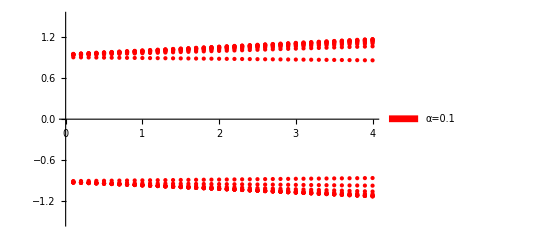

```mathematica
f3=ListPlot[data,PlotRange->{{0,4},{-1.5,1.5}},PlotStyle->Red,PlotLegends->SwatchLegend[{Red},{"α=0.1"}]]
```

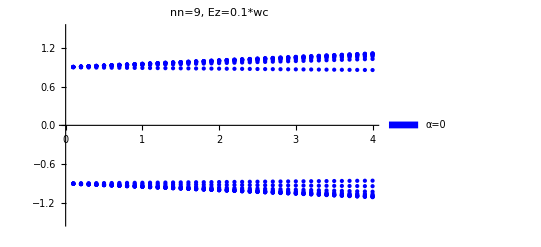

```mathematica
f2=ListPlot[data,PlotRange->{{0,4},{-1.5,1.5}},PlotStyle->Blue,PlotLegends->SwatchLegend[{Blue},{"α=0"}],PlotLabel->"nn=9, Ez=0.1*wc"]
```

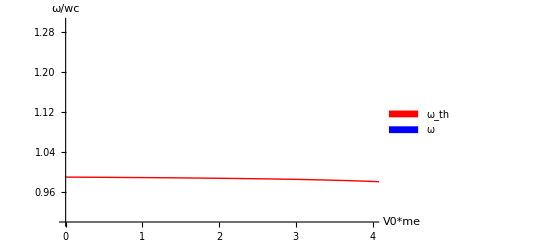

```mathematica
Show[f2,f1]
```

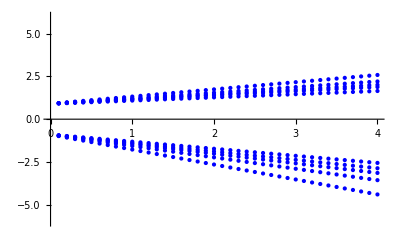

```mathematica
f1=ListPlot[data,PlotRange->{{0,4},{-6,6}},PlotStyle->Blue]
```

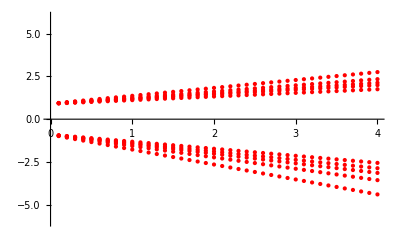

```mathematica
f2=ListPlot[data,PlotRange->{{0,4},{-6,6}},PlotStyle->Red]
```

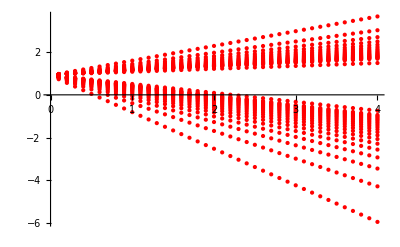

```mathematica
f2=ListPlot[data,PlotRange->{{0,4},Automatic},PlotStyle->Red]
```

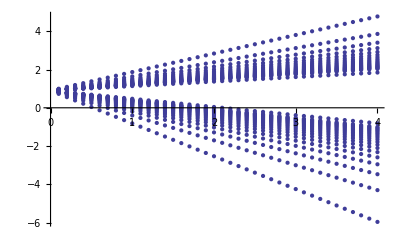

```mathematica
f1=ListPlot[data,PlotRange->{{0,4},Automatic}]
```

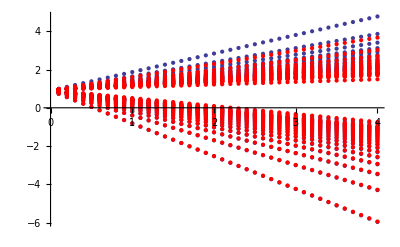

```mathematica
Show[f1,f2]
```

```mathematica
smatrix
```

{{-3.75342,0},{0,3.75342}}

```mathematica
Clear[n,m]
```

```mathematica
n=0;m=0;Cos[θ[n]/2]*Sin[θ[n]/2]*Cos[θ[m]/2]*Sin[θ[m]/2]*(1/l)*(P1[[n+2,m+2]]+P1[[n+1,m+1]])+(Sin[θ[n]/2]^2*Sin[θ[m]/2]^2+Cos[θ[n]/2]^2*Cos[θ[m]/2]^2)*P2[[n+1,m+1]]
```

0.199471

```mathematica
s[0,0]
```

-3.75342

```mathematica
ΔΣ[0,0]
```

0.401002

```mathematica
smatrix
```

{{0.401002}}